Power::infy: 碰到无穷表达式 1/0..

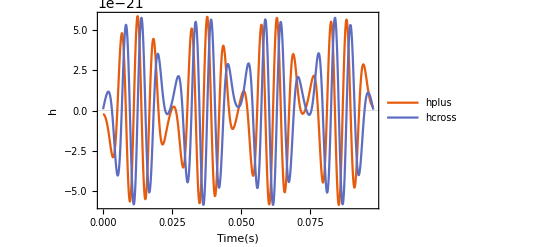

```mathematica
G=6.67*10^-8;
c=3*10^10;
r=3.0857*10^21;
i=0;(*inclination angle*)
n=2;(*number of free precession period *)
I0=10^45;(*moment of inertia*)
σ=π/4;(*initial wobble angle*)
ω0=200;(*initial angular velocity in body frame*)
I1=1*I0;
I2=2*I0;
I3=3*I0;
Δ1=I2-I3;
Δ2=I3-I1;
Δ3=I1-I2;
a=ω0*Sin[σ];
w20=0;
b=ω0*Cos[σ];
J= (I1^2*a^2+I2^2*w20^2+I3^2*b^2)^0.5;
E0=1/2 I1*a^2+1/2 I2*w20^2+1/2 I3*b^2;
k2=((I2-I1)(2E0*I3-J^2))/((I3-I2)(J^2-2E0*I1));
taut=√(((I3-I2)(J^2-2E0*I1))/(I1*I2*I3));
K=EllipticK[k2];
T=4*K*((I1*I2*I3)/((I3-I2)*(J^2-2*E0*I1)))^0.5;
dt=0.0001;
x1=I* (I3*b)/(I1*a);
α= Re[InverseJacobiSN[x1,k2]/I/K/2];
q= Exp[-π* EllipticK[1-k2]/EllipticK[k2]];
T1=2π/Re[(J/I1-2*I/T*EllipticThetaPrime[4,π*α*I,q]/EllipticTheta[4,π*α*I,q])];
w1=Table[a*JacobiCN[t*taut,k2],{t,0,n*T,dt}];
w2=Table[a*√((I1(I3-I1))/(I2(I3-I2)))*JacobiSN[t*taut,k2],{t,0,n*T,dt}];
w3=Table[b*JacobiDN[t*taut,k2],{t,0,n*T,dt}];
time=Table[t,{t,0,n*T,dt}];
A11=2*(Δ2*w2^2-Δ3*w3^2);
A22=2*(Δ3*w3^2-Δ1*w1^2);
A33=2*(Δ1*w1^2-Δ2*w2^2);
A12=(Δ1-Δ2+Δ3^2/I3)w1*w2;
A21=A12;
A13=(Δ3-Δ1+Δ2^2/I2)w1*w3;
A31=A13;
A23=(Δ2-Δ3+Δ1^2/I1)w2*w3;
A32=A23;
cosθ=Table[I3*b/J*JacobiDN[t*taut,k2],{t,0,n*T,dt}];
sinθ=Sin[ArcCos[Table[I3*b/J*JacobiDN[t*taut,k2],{t,0,n*T,dt}]]];
cosψ=Cos[ArcTan[Table[√((I1(I3-I2))/(I2(I3-I1)))JacobiCN[t*taut,k2]/JacobiSN[t*taut,k2],{t,0,n*T,dt}]]]*Sign[Floor[time/T]*T+T/2-time];
sinψ=Sin[ArcTan[Table[√((I1(I3-I2))/(I2(I3-I1)))JacobiCN[t*taut,k2]/JacobiSN[t*taut,k2],{t,0,n*T,dt}]]]*Sign[Floor[time/T]*T+T/2-time];
cosϕ1=Cos[ArcCos[Table[Re[EllipticTheta[4,2*π/T*t-π*α*I,q]/EllipticTheta[4,2*π/T*t+π*α*I,q]],{t,0,n*T,dt}]]/2];
sinϕ1=Sin[ArcSin[Table[Im[EllipticTheta[4,2*π/T*t-π*α*I,q]/EllipticTheta[4,2*π/T*t+π*α*I,q]],{t,0,n*T,dt}]]/2];
sinϕ2=Sin[Re[Table[(J/I1-2*I/T*EllipticThetaPrime[4,π*α*I,q]/EllipticTheta[4,π*α*I,q])*t,{t,0,n*T,dt}]]];
cosϕ2=Cos[Re[Table[(J/I1-2*I/T*EllipticThetaPrime[4,π*α*I,q]/EllipticTheta[4,π*α*I,q])*t,{t,0,n*T,dt}]]];
cosϕ=cosϕ1*cosϕ2-sinϕ1*sinϕ2;
sinϕ=sinϕ1*cosϕ2+cosϕ1*sinϕ2;
R11=cosψ*cosϕ-cosθ*sinψ*sinϕ;
R12=-sinψ*cosϕ-cosθ*cosψ*sinϕ;
R13=sinθ*sinϕ;
R21=cosψ*sinϕ+cosθ*sinψ*cosϕ;
R22=-sinψ*sinϕ+cosθ*cosψ*cosϕ;
R23=-sinθ*cosϕ;
R31=sinθ*sinψ;
R32=sinθ*cosψ;
R33=cosθ;
plus11=((Cos[i]R21-Sin[i]R31)*(Cos[i]R21-Sin[i]R31)-R11*R11)*A11;
plus12=((Cos[i]R21-Sin[i]R31)*(Cos[i]R22-Sin[i]R32)-R11*R12)*A12;
plus13=((Cos[i]R21-Sin[i]R31)*(Cos[i]R23-Sin[i]R33)-R11*R13)*A13;
plus21=((Cos[i]R22-Sin[i]R32)*(Cos[i]R21-Sin[i]R31)-R12*R11)*A21;
plus22=((Cos[i]R22-Sin[i]R32)*(Cos[i]R22-Sin[i]R32)-R12*R12)*A22;
plus23=((Cos[i]R22-Sin[i]R32)*(Cos[i]R23-Sin[i]R33)-R12*R13)*A23;
plus31=((Cos[i]R23-Sin[i]R33)*(Cos[i]R21-Sin[i]R31)-R13*R11)*A31;
plus32=((Cos[i]R23-Sin[i]R33)*(Cos[i]R22-Sin[i]R32)-R13*R12)*A32;
plus33=((Cos[i]R23-Sin[i]R33)*(Cos[i]R23-Sin[i]R33)-R13*R13)*A33;
hplus=-G/(c^4 r)(plus11+plus12+plus13+plus21+plus22+plus23+plus31+plus32+plus33);
cross11=(Cos[i]R21-Sin[i]R31)*R11 *A11;
cross12=(Cos[i]R21-Sin[i]R31)*R12 *A12;
cross13=(Cos[i]R21-Sin[i]R31)*R13 *A13;
cross21=(Cos[i]R22-Sin[i]R32)*R11 *A21;
cross22=(Cos[i]R22-Sin[i]R32)*R12 *A22;
cross23=(Cos[i]R22-Sin[i]R32)*R13 *A23;
cross31=(Cos[i]R23-Sin[i]R33)*R11 *A31;
cross32=(Cos[i]R23-Sin[i]R33)*R12 *A32;
cross33=(Cos[i]R23-Sin[i]R33)*R13 *A33;
hcross=(2G)/(c^4 r)(cross11+cross12+cross13+cross21+cross22+cross23+cross31+cross32+cross33);
first=Transpose@{time,hplus};
second=Transpose@{time,hcross};
large0=Transpose@{time,hplus,hcross};
Export["desktop/waveform.dat",large0];

ListPlot[{first,second},Joined->True,PlotTheme->"Scientific",LabelStyle->{18,GrayLevel[0]},FrameLabel->{{HoldForm[h],None},{HoldForm[Time [s]],None}},PlotLegends->{"hplus","hcross"}]
```

```mathematica
T
```

0.0490426

```mathematica
T1
```

0.012662

0.0179067